```mathematica
(*f [list_] := Module[{},
Print[list//FullForm];
Print["input list length = ", Length[list]];
equalReplace = <|"="->"=="|>;
list = StringReplace[#,"="->"=="]& @ list;
Print["List Updated = ", list];
list = ToExpression @ Flatten @ StringSplit[#,","]& @ list;
Print["List Edited = ", list];
Print["output list length = ", Length[list]];
(*Return[listEdited]
Length[listEdited];
displayEquationSystem[listEdited]*)
];
g[list_, element_] := Module[{},
If[Not[SameQ[list, {}]],list={}];
list = Insert[list, element,1];
];
SetAttributes[g,HoldAll]
SetAttributes[f, HoldAll]*)

expressionsList = {};
Grid@{{InputField[Dynamic[Null,oneElementList[expressionsList,#]&],String,FieldSize->{40, 3}],Button["Reset",expressionsList={}]}}
(*expressionsList =ToExpression @ Flatten @ StringSplit[#,","]& @ expressionsList *)
Dynamic[expressionsList]
Dynamic[displayEquationSystem[expressionsList]]
Button["Chiama f!",stringInputToSystem[expressionsList]]
```

| Reset

Chiama f!

```mathematica
emptyList = {};
SameQ[emptyList, {}]
```

True

```mathematica
Dynamic[risultato]//MatrixForm
Dynamic[displayEquationSystem[risultato]]
Dynamic[highlightElementsTable[risultato]]
```

```mathematica
expressionsList //FullForm
```

List[]

```mathematica
risultato = ToExpression @ Flatten @ StringSplit[#,","]& @ expressionsList
Length[risultato]
Solve[risultato]
risultato // FullForm
```

{}

0

{{}}

List[]

```mathematica
matriceProva = {{1,2},{3,4}};
{lu, p, c} = LUDecomposition[matriceProva];
l = lu SparseArray[{i_,j_}/;j<i->1,{2,2}]+IdentityMatrix[2] //MatrixForm
u = lu SparseArray[{i_,j_}/;j≥i->1,{2,2}]//MatrixForm
```

(1 | 0
3 | 1)

(1 | 2
0 | -2)

```mathematica
toggle[status_]:=Module[{},Return[Not[status]]];
verde = RGBColor[0,1,0,0.2];
rosso = RGBColor[1,0,0,0.2];
b = {0,1,0,0,0,0,0,0,1};
shown = False;

dim=3;a=ConstantArray[0,dim*3];
attributiCondizionali := {};
bla = Partition[Table[With[{i=i},Dynamic[Framed[InputField[Dynamic[a[[i]]],FieldSize->{2,1},Appearance->"Frameless",Background->If[shown,If[SameQ[a[[i]],b[[i]]],verde,rosso]]],FrameStyle->If[shown,If[SameQ[a[[i]],b[[i]]],verde,rosso],Automatic],FrameMargins->None]]],{i,dim*3}],dim];
(*bla[[2,1]] = 0;*)
For[i=2,i≤Length[bla],i++,
bla[[i]][[1;;i-1]]=0;
];
(*bla[[3]][[1;;2]] = 0;*)
bla//MatrixForm
Button["Toggle!",shown=toggle[shown]]
```

( |  | 
0 |  | 
0 | 0 | )

Toggle!

```mathematica
Dynamic[a]
```

```mathematica
sistema = {3x-y,4x-y+z+t-s};
 sorted = Sort[Variables[sistema]]
p = CoefficientRules[sistema,sorted]
Values[p]
Lookup[p[[1]],Key[{0,0,1,0,0}]]
esempioEq2 = Sort[Keys[p[[2]]]]
```

{s,t,x,y,z}

{{{0,0,1,0,0}→3,{0,0,0,1,0}→-1},{{1,0,0,0,0}→-1,{0,1,0,0,0}→1,{0,0,1,0,0}→4,{0,0,0,1,0}→-1,{0,0,0,0,1}→1}}

{{3,-1},{-1,1,4,-1,1}}

3

{{0,0,0,0,1},{0,0,0,1,0},{0,0,1,0,0},{0,1,0,0,0},{1,0,0,0,0}}

```mathematica
Flatten@Position[esempioChiave,1]
```

{}

```mathematica
Flatten@Position[Variables[sistema],k]
```

{}

```mathematica
variabili = Sort[Variables[sistema]]
rules = CoefficientRules[sistema,variabili]
matrix = {};
For[i=1,i≤Length[rules],i++,
Print["Rules per equazione ",i," = ", rules[[i]]];
row = {};
For[j=1,j≤Length[variabili],j++,
chiave = Normal[SparseArray[{j->1},Length[variabili]]];
If[MemberQ[Keys[rules[[i]]],chiave],
Print["L'incognita ", variabili[[j]], " C'E' nell'equazione"];AppendTo[row,Lookup[rules[[i]],Key[chiave]]],Print["L'incognita ", variabili[[j]], " NON C'E' nell'equazione"];AppendTo[row,0]
]
];
AppendTo[matrix,row];
]
Print[matrix]
matrix //MatrixForm
vect = {s,t,x,y,z}
r = Dot[matrix, vect]
MatchQ[r,sistema]
```

{s,t,x,y,z}

{{{0,0,1,0,0}→3,{0,0,0,1,0}→-1},{{1,0,0,0,0}→-1,{0,1,0,0,0}→1,{0,0,1,0,0}→4,{0,0,0,1,0}→-1,{0,0,0,0,1}→1}}

Rules per equazione 1 = {{0,0,1,0,0}→3,{0,0,0,1,0}→-1}

L'incognita s NON C'E' nell'equazione

L'incognita t NON C'E' nell'equazione

L'incognita x C'E' nell'equazione

L'incognita y C'E' nell'equazione

L'incognita z NON C'E' nell'equazione

Rules per equazione 2 = {{1,0,0,0,0}→-1,{0,1,0,0,0}→1,{0,0,1,0,0}→4,{0,0,0,1,0}→-1,{0,0,0,0,1}→1}

L'incognita s C'E' nell'equazione

L'incognita t C'E' nell'equazione

L'incognita x C'E' nell'equazione

L'incognita y C'E' nell'equazione

L'incognita z C'E' nell'equazione

{{0,0,3,-1,0},{-1,1,4,-1,1}}

(0 | 0 | 3 | -1 | 0
-1 | 1 | 4 | -1 | 1)

{s,t,x,y,z}

{3 x-y,-s+t+4 x-y+z}

True

```mathematica
MatchQ[Normal[SparseArray[{5->1},Length[Variables[sistema]]]],{0,0,0,1,0}]
```

False

```mathematica
lista = {{0,0,1,0,0}->3, {0,0,0,1,0}->-1}
```

{{0,0,1,0,0}→3,{0,0,0,1,0}→-1}

```mathematica
MemberQ[Keys[lista], {0,0,1,0,0}]
```

True

```mathematica
linearSystem2= {7x+6y+5z,-4y+2z ,-5x+6y}
```

{7 x+6 y+5 z,-4 y+2 z,-5 x+6 y}

```mathematica
Level[#,1][[1]]& /@ linearSystem2
```

{7 x,-4 y,-5 x}

```mathematica
Level[#,1][[2]] & /@ linearSystem2
```

{6 y,2 z,6 y}

```mathematica
eq = 3x-2y
```

3 x-2 y

```mathematica
eq//FullForm
```

Plus[Times[3,x],Times[-2,y]]

```mathematica
Head[eq]
```

Plus

```mathematica
SameQ[Head[eq],Equal]
```

False

```mathematica
Variables[{3x-2y==1}]
```

{}

```mathematica
RowReduce[{{1,2},{3,4}}]//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
{lu,p,c} = LUDecomposition[{{1,2},{3,4}}]
U = UpperTriangularize[lu]
L = lu SparseArray[{i_,j_}/;j<i->1,{2,2}]+IdentityMatrix[2]
L.U
Inverse[L].{3,-1}
LinearSolve[{{1,2},{3,4}},{3,-1}]
```

{{{1,2},{3,-2}},{1,2},0}

{{1,2},{0,-2}}

{{1,0},{3,1}}

{{1,2},{3,4}}

{3,-10}

{-7,5}

```mathematica
A = {{1,1,4,-1},{1,0,-1,0},{1,-2,4,0},{2,0,3,-3}};
A//MatrixForm
{lu,p, c} = LUDecomposition[A]
U=Normal[lu SparseArray[{i_,j_}/;j≥i->1,{4,4}]];
L = lu SparseArray[{i_,j_}/;j<i->1,{4,4}]+IdentityMatrix[4];
U //MatrixForm
L // MatrixForm
Permute[L.U,p]
SameQ[Permute[L.U,p], A]
```

(1 | 1 | 4 | -1
1 | 0 | -1 | 0
1 | -2 | 4 | 0
2 | 0 | 3 | -3)

{{{1,1,4,-1},{1,-1,-5,1},{2,2,5,-3},{1,3,3,7}},{1,2,4,3},0}

(1 | 1 | 4 | -1
0 | -1 | -5 | 1
0 | 0 | 5 | -3
0 | 0 | 0 | 7)

(1 | 0 | 0 | 0
1 | 1 | 0 | 0
2 | 2 | 1 | 0
1 | 3 | 3 | 1)

{{1,1,4,-1},{1,0,-1,0},{1,-2,4,0},{2,0,3,-3}}

True

```mathematica
Solve[{3x-2y+1==0,4x-5y==-2}]
```

{{x→-1/7,y→2/7}}

```mathematica
Solve[{x+5y==3,2x-4y==-8}]
```

{{x→-2,y→1}}

```mathematica
Solve[{2x-5y==7,x-3y==1}]
```

{{x→16,y→5}}

```mathematica
Solve[{2x-y==0,x+3y==1}]
```

{{x→1/7,y→2/7}}

```mathematica
Solve[{3x-2y+z==0,x-y+z==0,4x+2y-3z==5}]
```

{{x→1,y→2,z→1}}

```mathematica
Solve[{x+y-z==6,x+y==3,x+z==0}]
```

{{x→3,y→0,z→-3}}

```mathematica
Solve[{3x+y+z==3,6x-2y+z==1,3x+3y+3z==7}]
```

{{x→1/3,y→1,z→1}}

```mathematica
Solve[{x+2y+3z==1,3x+4y+6z==3,10x+5y-3z==-4}]
```

{{x→1,y→-2,z→4/3}}

```mathematica
A = {{1,2},{3,4}};
LUFactor[n_]:=Module[{i,j,k,p,Z},
r = Table[j,{j,n}];
For[p=1,p≤n-1,p++,
For[j=p+1,j≤n,j++,
If[Abs[A_[[r[[j]],p]]]>Abs[A_[[r[[p]],p]]],r_[[{j,p}]]=r_[[{p,j}]]];];
For[k=p+1,k≤n,k++,
A_[[r[[k]],p]]= A_[[r[[k]],p]]/A_[[r[[p]],p]];
For[c=p+1,c≤n,c++,
A_[[r[[k]],c]]= A_[[r[[k]],c]]-A_[[r[[k]],p]] A_[[r[[p]],c]];
];
];
];
L = P = IdentityMatrix[n];
P = P_[[r]];
U = A_[[r]];
For[i=1,i≤n,i++,
For[j=1,j≤i-1,j++,
L_[[i,j]]=A_[[r[[i]],j]];
U_[[i,j]]=0;
];
];
];
```

```mathematica
LUFactor[2]
```

```mathematica
A
```

{{1/3,2/3},{3,4}}

```mathematica
m = {{1,2,3},{1,4,9},{1,8,27}};
{lu,p,c} = LUDecomposition[m]
U = Normal[lu SparseArray[{i_,j_}/;j≥i->1,{3,3}]];
U // MatrixForm
```

{{{1,2,3},{1,2,6},{1,3,6}},{1,2,3},0}

(1 | 2 | 3
0 | 2 | 6
0 | 0 | 6)

```mathematica
RowReduce[m]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
m = {{1,2,3},{4,5,6},{7,8,9}};
m//MatrixForm
Permute[m,Cycles[{{1,3}}]]//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

(7 | 8 | 9
4 | 5 | 6
1 | 2 | 3)

```mathematica
LUFactor2[A0_,n_]:=Module[{A,k,j,i},
A = A0;
For[p=1,p≤n-1,p++,
Block[{},
For[k=p+1,k≤n,k++,
A[[k,p]] = A[[k,p]]/A[[p,p]];
For[j=p+1,j≤n,k++,
A[[k,j]] = A[[k,j]]-A[[k,p]]A[[p,j]];
];
];
];
LNuovo = A;
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
LNuovo[[i,j]] = 0;
];
];
For[i=1,i≤n,i++,LNuovo[[i,i]] = 1;];
UNuovo = A;
For[i=1,i≤n,i++,
For[j=1,j≤i-1,j++,
UNuovo[[i,j]] = 0;
];
];
];
Return[LNuovo,UNuovo];
];
```

```mathematica
A//MatrixForm
```

(1/3 | 2/3
3 | 4)

```mathematica
Max[A[[All,1]]]
```

3

```mathematica
matrice = {{1,1,4,-1,9},{1,0,-1,0,1},{1,-2,4,0,6},{2,0,3,-3,8}};
matrice//MatrixForm
```

(1 | 1 | 4 | -1 | 9
1 | 0 | -1 | 0 | 1
1 | -2 | 4 | 0 | 6
2 | 0 | 3 | -3 | 8)

```mathematica
pivot = Max[Abs[matrice[[All,2]][[2;;]]]]
```

2

```mathematica
matrice[[All,2]][[2;;]]
```

{0,-2,0}

```mathematica
index =Flatten[FirstPosition[matrice[[All,1]],Max[matrice[[All,1]]]]]
```

{4}

```mathematica
matrice=Permute[matrice,Cycles[{Flatten[{2,index}]}]];
matrice//MatrixForm
```

(1 | 1 | 4 | -1 | 9
2 | 0 | 3 | -3 | 8
1 | -2 | 4 | 0 | 6
1 | 0 | -1 | 0 | 1)

```mathematica
lambda = -matrice[[2,1]]/pivot
```

-1

```mathematica
matrice[[2]]+lambda*matrice[[1]]
```

{1,-1,-1,-2,-1}

```mathematica
2*matrice[[2]]-matrice[[1]]
```

{3,-1,2,-5,7}

```mathematica
FattorizzazioneLU[A_,b_]:=Module[{L,U,P,bPerm,matriceEdited,n,pivot,candidatePivot,subColonna,pivotIndex,lambda,i,k},
If[SameQ[Det[A],0],Return[{Null,Null,Null,Null}]];

n = Length[A];
matriceEdited = A;
P = IdentityMatrix[n];
L = ArrayReshape[ConstantArray[0,n*n],{n, n}];
For[i=1,i<n,i++,
subColonna = matriceEdited[[All,i]][[i;;]];
candidatePivot = Max[Abs[subColonna]];
pivotIndex = FirstPosition[Abs[matriceEdited[[All,i]]],candidatePivot][[1]];
pivot=matriceEdited[[pivotIndex,i]];
If[Not[Equal[i,pivotIndex]],
matriceEdited = Permute[matriceEdited,Cycles[{{i,pivotIndex}}]];
P = Permute[P, Cycles[{Flatten[{i,pivotIndex}]}]];
];
For[k=i+1,k≤n,k++,
If[Not[Equal[matriceEdited[[k,i]],0]], (* PROVA; SERVE CONTROLLO SU PIVOT = 0 *)
lambda = (matriceEdited[[k,i]]/pivot);
L[[k,i]] = lambda;
matriceEdited[[k]] = matriceEdited[[k]]-lambda*matriceEdited[[i]];
];
];
If[Not[Equal[i,pivotIndex]]&&i≥2,
pivotIndex = pivotIndex-i+1;
L[[i;;n,1;;i-1]]=Permute[L[[i;;n,1;;i-1]],Cycles[{{1,pivotIndex}}]];
];
];
U = matriceEdited;
L=L+IdentityMatrix[n];
bPerm = Inverse[L].P.b;
Return[{L,U,P,bPerm}];
];
```

```mathematica
matrice = {{1,1,4,-1,9},{1,0,-1,0,1},{1,-2,4,0,6},{2,0,3,-3,8}};
matrice2 = {{4,0,1,1},{3,1,3,1},{0,1,2,0},{2,2,4,1}};
matrice3 = {{1,2,3},{4,5,6},{7,8,9}};
impossibile = {{1,1},{1,1}};
impossibileB = {3,1};
indeterminato = {{1,1},{1,1}};
indeterminatoB = {3,3};
{L,U,P,bPrimo} = FattorizzazioneLU[matrice2,{1,2,3,4}];
Print["L = ", L//MatrixForm, " U = ", U//MatrixForm, " b' = ", bPrimo//MatrixForm, " P = ", P//MatrixForm]
Print["PA = ", P.matrice2//MatrixForm, " LU = ", L.U//MatrixForm, " Sono uguali? ", MatchQ[P.matrice2, L.U]]
LinearSolve[matrice2,{1,2,3,4}]
LinearSolve[U,bPrimo]
(*LinearSolve[impossibile,impossibileB]
Det[impossibile]
LinearSolve[indeterminato,indeterminatoB]
Det[indeterminato]*)
```

L = (1 | 0 | 0 | 0
1/2 | 1 | 0 | 0
3/4 | 1/2 | 1 | 0
0 | 1/2 | 1/2 | 1) U = (4 | 0 | 1 | 1
0 | 2 | 7/2 | 1/2
0 | 0 | 1/2 | 0
0 | 0 | 0 | -1/4) b' = (1
7/2
-1/2
3/2) P = (1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

PA = (4 | 0 | 1 | 1
2 | 2 | 4 | 1
3 | 1 | 3 | 1
0 | 1 | 2 | 0) LU = (4 | 0 | 1 | 1
2 | 2 | 4 | 1
3 | 1 | 3 | 1
0 | 1 | 2 | 0) Sono uguali? True

{2,5,-1,-6}

{2,5,-1,-6}

```mathematica
Join[Drop[{{11,12,13},{21,22,23},{31,32,33}},None,-1],{{5},{5},{5}},2]//MatrixForm
```

(11 | 12 | 5
21 | 22 | 5
31 | 32 | 5)

```mathematica
p =Take[{{11,12,13},{21,22,23},{31,32,33}},All,2];
p // MatrixForm
```

(11 | 12
21 | 22
31 | 32)

```mathematica
termini = Take[{{11,12,13},{21,22,23},{31,32,33}},All,-1];
termini//MatrixForm
```

(13
23
33)

```mathematica
Join[p,termini,2]//MatrixForm
```

(11 | 12 | 13
21 | 22 | 23
31 | 32 | 33)

```mathematica
matrice2//MatrixForm
L = ArrayReshape[ConstantArray[0,4*4],{4,4}];
L // MatrixForm
matrice2[[All,1]]//MatrixForm
(*P = {{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}};
P//MatrixForm*)
matrice2[[All,2]]=Permute[matrice2[[All,2]],Cycles[{{2,4}}]]
matrice2//MatrixForm
```

(4 | 0 | 1 | 1
3 | 1 | 3 | 1
0 | 1 | 2 | 0
2 | 2 | 4 | 1)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(4
3
0
2)

{0,2,1,1}

(4 | 0 | 1 | 1
3 | 2 | 3 | 1
0 | 1 | 2 | 0
2 | 1 | 4 | 1)

```mathematica
{2,3,4}//FullForm
```

List[2,3,4]

```mathematica
Column@{2,3,4}
```

2
3
4

```mathematica
matrice2//MatrixForm
```

(4 | 0 | 1 | 1
3 | 2 | 3 | 1
0 | 1 | 2 | 0
2 | 1 | 4 | 1)

```mathematica
matrice2[[2;;,2;;]]//MatrixForm
```

(2 | 3 | 1
1 | 2 | 0
1 | 4 | 1)

```mathematica
indici = {{2,2},{5,3},{1,1}}
ind=StringReplace["xy", {"x"->ToString[#[[1]]],"y"->ToString[#[[2]]]}]& /@ indici
Subscript["a","indici"]/.{"indici"->#}& /@ ind
```

{{2,2},{5,3},{1,1}}

{22,53,11}

{a_22,a_53,a_11}

```mathematica
emptyList = {}
emptyList = Insert[emptyList,"Ciao", 1];
emptyList
emptyList= Insert[emptyList,"Ciao2", 2];
emptyList = Insert[emptyList, "Bla", 1];
emptyList
```

{}

{Ciao}

{Bla,Ciao,Ciao2}

```mathematica
emptyList = {Null, Null, Null}
emptyList[[1]] = "Ciao"
emptyList
emptyList[[3]] = "Bla"
emptyList
emptyList[[1]] = "Hello"
emptyList
```

{Null,Null,Null}

Ciao

{Ciao,Null,Null}

Bla

{Ciao,Null,Bla}

Hello

{Hello,Null,Bla}

```mathematica
s = Solve[{2x+3y==12,3x-y==7}]
{x,y} /. s
x
```

{{x→3,y→2}}

{{3,2}}

x

```mathematica
f[exp_]:=Module[{x},exp/.x->4]
```

```mathematica
f[2x+3y==12]
```

2 x+3 y==12

```mathematica
g[exp_]:=Block[{x},exp/.x->4]
```

```mathematica
g[2x+3y==12]
```

8+3 y==12

```mathematica
f2[exp_]:=Module[{x,sol},sol=Solve[exp];Plot[y/.Solve[exp],{x,-10,10}]]
```

```mathematica
f2[2x+3y==12]
```

-Graphics-

```mathematica
g2[exp_]:=Block[{x,y,sol},sol=Solve[exp];Plot[y/.Solve[exp],{x,-10,10}]]
```

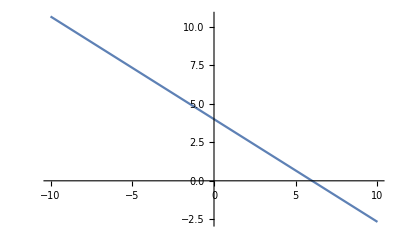

```mathematica
g2[2x+3y==12]
```

```mathematica
exerciseFinalGauss[]
```

checkButtonSystemToMatrix

IF

2

choice = {x==-9/20
y==-18

answer = {x==-2,y==1}

choice = {x==-2
y==1

answer = {x==-2,y==1}

```mathematica
step = 0;
shown = False;
button = Button["Cliccami!", step++]
Grid[{{Dynamic[Switch[step,
0, "Passo 0",
1, "Passo 1";shown=True, 
2, "Passo 2",
3, "Passo 3";shown=False]]}}]
Dynamic[shown]
```

Cliccami!

```mathematica
ClearAll[a,b];
system = {2a-4b+c==-8,a+5b-2c==3,a+b+c==2};
solutions = Solve[system]
solutions = {{a->5, b->2/3}}
lhss = Level[#, 1][[1]]&/@system;
vars = Variables[lhss];
aSol = StandardForm[vars[[1]]]==(vars[[1]] /. solutions[[1]]);
bSol = StandardForm[vars[[2]]]==(vars[[2]] /. solutions[[1]]);
sol1 = displayEquationSystem[{aSol,bSol}]
sol2 = displayEquationSystem[{bSol, aSol}]
MatchQ[sol1, sol2]
StandardForm[#]==(# /. solutions[[1]])& /@vars;
```

{{a→-35/22,b→37/22,c→21/11}}

{{a→5,b→2/3}}

{a==5
b==2/3

{b==2/3
a==5

False

```mathematica
RandomInteger[{-20,20}]/RandomInteger[{1,20}]
```

1/9

```mathematica
finalExerciseRandomAnswers[system]
```

choice = {a==-9
b==3
c==6/7

answer = {a==-35/22,b==37/22,c==21/11}

choice = {a==-35/22
b==37/22
c==21/11

answer = {a==-35/22,b==37/22,c==21/11}